This notebook produces plots of the orbits generated by local complementation orbit up to and including 8 qubits, where isomorphic are not considered as equal (unless they are equal).

This work refers to the work “title goes here”, https://arxiv.org/abs/XXXX.XXXXX. Please see this work for assosciated documentation.

You can choose to import from .mx or .csv. Importing data from .mx is faster, but may not be possible on older versions of Mathematica. Importing from .csv is broken up into qubit number as it can be slow for large number of qubits. Feel free to just import the qubit number you are interested in.

## Load data

### Import data from ‘.csv’

#### Init

```mathematica
SetDirectory[NotebookDirectory[]];

(* Graph state display options*)
defcol=ColorData[97,"ColorList"][[7]];
graphsize=100;
vertexsize=0.30;
edgethickness =0.024;
impad=10;

(* precompiled import for csv *)
len4={5,11};
len5={6,14,30,132}
len6={7,17,18,38,39,82,40,41,176,372,132};
len7={8,20,22,46,48,48,50,104,106,108,224,50,52,220,110,232,112,236,492,484,1052,504,1056,532,1096,528};
len8={9,23,26,54,27,58,57,61,126,62,130,64,132,134,136,138,284,288,135,139,290,294,612,60,62,63,264,66,138,288,140,140,142,142,296,612,308,300,644,616,145,149,616,302,314,648,306,640,306,656,648,1320,1380,1356,2932,300,312,652,148,636,318,151,318,1368,668,668,660,1408,1404,1380,1428,1424,2952,3004,3024,152,692,680,149,680,1424,1448,1436,1468,3032,3092,3088,2904,660,704,1468,3072,3156,1452,3160,532,3156,1492,1628,3168,3248};


fourCiorbit=Range[2];
fourCigraphlists=Table[0,{i,Range[2]},{j,len4[[i]]}];
four=4;

fiveCiorbit=Range[4];
fiveCigraphlists=Table[0,{i,Range[4]},{j,len5[[i]]}];
five=5;

sixCiorbit=Range[11];
sixCigraphlists=Table[0,{i,Range[11]},{j,len6[[i]]}];
six=6;

sevenCiorbit=Range[26];
sevenCigraphlists=Table[0,{i,Range[26]},{j,len7[[i]]}];
seven=7;

eightCiorbit=Range[101];
eightCigraphlists=Table[0,{i,Range[101]},{j,len8[[i]]}];
eight=8;
```

{6,14,30,132}

#### 4 qubit

```mathematica
fourCidat=ToString@Import["4qubitorbitsLi.csv"];
fourCidat=StringReplace[fourCidat,"("->"{"];
fourCidat=StringReplace[fourCidat,")"->"}"];
fourCidat=StringReplace[fourCidat,"-"->"->"];
fourCidat=ToExpression@fourCidat;

Do[
fourCiorbit[[i]]=Graph[
Range[fourCidatᵀ[[2]][[i]]],
fourCidatᵀ[[3]][[i]],EdgeLabels->Thread[fourCidatᵀ[[4]][[i]]ᵀ[[1]]->fourCidatᵀ[[4]][[i]]ᵀ[[2]]]
];
,{i,Length@fourCiorbit}];

Do[
fourCigraphlists[[i]][[j]]=Graph[
Range[four],
fourCidat[[i]][[5]][[j]]
];
fourCigraphlists[[i]][[j]]=UndirectedGraph[fourCigraphlists[[i]][[j]],GraphLayout->"CircularEmbedding",
ImagePadding->impad,
ImageSize->graphsize,
VertexSize->vertexsize,
EdgeStyle->{Thickness[edgethickness]},
VertexStyle->{},
VertexLabels->None];
,{i,Length@fourCidat},{j,Length@fourCidat[[i]][[5]]}];
```

#### 5 qubit

```mathematica
fiveCidat=ToString@Import["5qubitorbitsLi.csv"];
fiveCidat=StringReplace[fiveCidat,"("->"{"];
fiveCidat=StringReplace[fiveCidat,")"->"}"];
fiveCidat=StringReplace[fiveCidat,"-"->"->"];
fiveCidat=ToExpression@fiveCidat;

Do[
fiveCiorbit[[i]]=Graph[
Range[fiveCidatᵀ[[2]][[i]]],
fiveCidatᵀ[[3]][[i]],EdgeLabels->Thread[fiveCidatᵀ[[4]][[i]]ᵀ[[1]]->fiveCidatᵀ[[4]][[i]]ᵀ[[2]]]
];
,{i,Length@fiveCiorbit}];

Do[
fiveCigraphlists[[i]][[j]]=Graph[
Range[five],
fiveCidat[[i]][[5]][[j]]
];
fiveCigraphlists[[i]][[j]]=UndirectedGraph[fiveCigraphlists[[i]][[j]],GraphLayout->"CircularEmbedding",
ImagePadding->impad,
ImageSize->graphsize,
VertexSize->vertexsize,
EdgeStyle->{Thickness[edgethickness]},
VertexStyle->{},
VertexLabels->None];
,{i,Length@fiveCidat},{j,Length@fiveCidat[[i]][[5]]}];
```

#### 6 qubit

```mathematica
sixCidat=ToString@Import["6qubitorbitsLi.csv"];
sixCidat=StringReplace[sixCidat,"("->"{"];
sixCidat=StringReplace[sixCidat,")"->"}"];
sixCidat=StringReplace[sixCidat,"-"->"->"];
sixCidat=ToExpression@sixCidat;

Do[
sixCiorbit[[i]]=Graph[
Range[sixCidatᵀ[[2]][[i]]],
sixCidatᵀ[[3]][[i]],EdgeLabels->Thread[sixCidatᵀ[[4]][[i]]ᵀ[[1]]->sixCidatᵀ[[4]][[i]]ᵀ[[2]]]
];
,{i,Length@sixCiorbit}];

Do[
sixCigraphlists[[i]][[j]]=Graph[
Range[six],
sixCidat[[i]][[5]][[j]]
];
sixCigraphlists[[i]][[j]]=UndirectedGraph[sixCigraphlists[[i]][[j]],GraphLayout->"CircularEmbedding",
ImagePadding->impad,
ImageSize->graphsize,
VertexSize->vertexsize,
EdgeStyle->{Thickness[edgethickness]},
VertexStyle->{},
VertexLabels->None];
,{i,Length@sixCidat},{j,Length@sixCidat[[i]][[5]]}];
```

#### 7 qubit

```mathematica
sevenCidat=ToString@Import["7qubitorbitsLi.csv"];
sevenCidat=StringReplace[sevenCidat,"("->"{"];
sevenCidat=StringReplace[sevenCidat,")"->"}"];
sevenCidat=StringReplace[sevenCidat,"-"->"->"];
sevenCidat=ToExpression@sevenCidat;

Do[
sevenCiorbit[[i]]=Graph[
Range[sevenCidatᵀ[[2]][[i]]],
sevenCidatᵀ[[3]][[i]],EdgeLabels->Thread[sevenCidatᵀ[[4]][[i]]ᵀ[[1]]->sevenCidatᵀ[[4]][[i]]ᵀ[[2]]]
];
,{i,Length@sevenCiorbit}];

Do[
sevenCigraphlists[[i]][[j]]=Graph[
Range[seven],
sevenCidat[[i]][[5]][[j]]
];
sevenCigraphlists[[i]][[j]]=UndirectedGraph[sevenCigraphlists[[i]][[j]],GraphLayout->"CircularEmbedding",
ImagePadding->impad,
ImageSize->graphsize,
VertexSize->vertexsize,
EdgeStyle->{Thickness[edgethickness]},
VertexStyle->{},
VertexLabels->None];
,{i,Length@sevenCidat},{j,Length@sevenCidat[[i]][[5]]}];
```

#### 8 qubit (takes a few minutes)

```mathematica
eightCidat=Import["8qubitorbitsLi.csv"];
Print["Import successfull. Converting to string for processing.."];
eightCidat=ToString@eightCidat
Print["Successfull. Processing string.."];
eightCidat=StringReplace[eightCidat,"("->"{"];
eightCidat=StringReplace[eightCidat,")"->"}"];
eightCidat=StringReplace[eightCidat,"-"->"->"];
eightCidat=ToExpression@eightCidat;

Do[
eightCiorbit[[i]]=Graph[
Range[eightCidatᵀ[[2]][[i]]],
eightCidatᵀ[[3]][[i]],EdgeLabels->Thread[eightCidatᵀ[[4]][[i]]ᵀ[[1]]->eightCidatᵀ[[4]][[i]]ᵀ[[2]]]
];
,{i,Length@eightCiorbit}];

Do[
eightCigraphlists[[i]][[j]]=Graph[
Range[eight],
eightCidat[[i]][[5]][[j]]
];
eightCigraphlists[[i]][[j]]=UndirectedGraph[eightCigraphlists[[i]][[j]],GraphLayout->"CircularEmbedding",
ImagePadding->impad,
ImageSize->graphsize,
VertexSize->vertexsize,
EdgeStyle->{Thickness[edgethickness]},
VertexStyle->{},
VertexLabels->None];
,{i,Length@eightCidat},{j,Length@eightCidat[[i]][[5]]}];
```

#### Initialise to one variable.

```mathematica
orbitsCi={{},{},{},fourCiorbit,fiveCiorbit,sixCiorbit,sevenCiorbit,eightCiorbit};
orbitsCigraphlist={{},{},{},fourCigraphlists,fiveCigraphlists,sixCigraphlists,sevenCigraphlists};

ClearAll[fourCidat,fiveCidat,sixCidat,sevenCidat,eightCidat,fourCiorbit,fiveCiorbit,sixCiorbit,sevenCiorbit,eightCiorbit,fourCigraphlists,fiveCigraphlists,sixCigraphlists,sevenCigraphlists];
```

### Import data from ‘.mx’

#### Import from Mathematica 11 ‘.mx’ (this may take 30s)

```mathematica
SetDirectory[NotebookDirectory[]];
orbitsCi=Import["orbitsCi.mx"];
orbitsCigraphlist=Import["orbitsCigraphlist.mx"];
```

## Functions

```mathematica
deleteIsoG1[gl_List]:=Module[{},DeleteDuplicates[gl,IsomorphicGraphQ]];

colourblender[one_,two_]:=Blend[{one,two},0.5]; 


plotOrbitCi[noqub_,myclass_]:=Module[{oedgelabels,theselabels,graphimgs,imsz,g1,graphlabelgraph,graphlabels,thisorbit},


(* Sanitise graphs for printing *)
Do[orbitsCigraphlist[[noqub]][[myclass]][[i]] =Graph[orbitsCigraphlist[[noqub]][[myclass]][[i]],ImagePadding->0],{i,Length@orbitsCigraphlist[[noqub]][[myclass]]}];

(* Sanitise orbit edge labels for printing *)
theselabels=Sort@(List@@@PropertyValue[orbitsCi[[noqub]][[myclass]],EdgeLabels]);
oedgelabels={};
Do[If[theselabels[[i]][[1]][[1]]<=theselabels[[i]][[1]][[2]],AppendTo[oedgelabels ,{ theselabels[[i]][[1]][[1]]<->theselabels[[i]][[1]][[2]],theselabels[[i]][[2]]}]],{i,Length@theselabels}];
oedgelabels=Thread[oedgelabelsᵀ[[1]]->oedgelabelsᵀ[[2]]];

(* get images of each graph state to plot on the vertices of the orbit *)
graphimgs=Range@Length@orbitsCigraphlist[[noqub]][[myclass]];
imsz=100;
Do[
(* graph state vertices labelled? *)
If[graphsvertexlabelledQ,g1=Graph[orbitsCigraphlist[[noqub]][[myclass]][[i]],VertexLabels->Thread[Range[noqub]->Range[noqub]],VertexSize->svsize,EdgeStyle->sesize,VertexLabelStyle->Directive[Black,vertexlabelfontsize]];
g1=SetProperty[g1,VertexLabels->(#->Placed[#2,{0.59,0.4}]&@@@(VertexLabels/.Options[g1]))];
,
g1=Graph[orbitsCigraphlist[[noqub]][[myclass]][[i]],VertexSize->svsize,EdgeStyle->sesize];
];
graphimgs[[i]] = Show[{g1,
Graphics[{Directive[Black,Thickness[gcirclethickness]],Circle[{0,0},gpadding]}]},ImageSize->imsz]
,{i,Length@orbitsCigraphlist[[noqub]][[myclass]]}];
graphlabelgraph=Thread[Range[Length@orbitsCigraphlist[[noqub]][[myclass]]]->graphimgs];

(* compute graph state labels *)
If[graphslabelledQ ,
graphlabels= Table[i->"G"<>ToString[i],{i,Length@orbitsCigraphlist[[noqub]][[myclass]]}],
graphlabels=Thread[Range@Length@orbitsCigraphlist[[noqub]][[myclass]]->Table[None,{i,Length@orbitsCigraphlist[[noqub]][[myclass]]}]];
];


If[orbitedgeslabelledQ,
thisorbit=UndirectedGraph[orbitsCi[[noqub]][[myclass]],VertexLabels->graphlabels,EdgeLabels->oedgelabels,VertexShape->graphlabelgraph,VertexSize->lvsize,EdgeStyle->lesize,EdgeLabelStyle->Directive[Black,edgefontsize](*,GraphLayout->"SpringEmbedding"*)];

If[graphslabelledQ ,thisorbit=SetProperty[thisorbit,VertexLabels->(#->Placed[#2,{0.51,0.29}]&@@@(VertexLabels/.Options[thisorbit]))];]
,
thisorbit=UndirectedGraph[orbitsCi[[noqub]][[myclass]],EdgeLabels->None,VertexShape->graphlabelgraph,VertexLabels->graphlabels,VertexSize->lvsize,EdgeStyle->lesize,EdgeLabelStyle->Directive[Black,edgefontsize](*,GraphLayout->"SpringEmbedding"*)];

If[graphslabelledQ ,thisorbit=SetProperty[thisorbit,VertexLabels->(#->Placed[#2,{0.51,0.29}]&@@@(VertexLabels/.Options[thisorbit]))];]
];

thisorbit];






plotOrbitMatrixCi[noqub_,myclass_]:=Module[{theselabels,oedgelabels,goodcolours,labels,colourlabel,mycolours,isocolours,isocolours2,gatheredisocols,isolens,isocount,colourisoadjmat,LCadj,isogroups,isomat,one,two,glo,glr,glos,bticks,arfaccumisolenssd,tickas,gl,btickstr,accumisolens,noedg,avar,orbitadj,orbitlegend,dist,distp,distleg},


(* Sanitise graphs for printing *)
Do[orbitsCigraphlist[[noqub]][[myclass]][[i]] =Graph[orbitsCigraphlist[[noqub]][[myclass]][[i]],ImagePadding->0],{i,Length@orbitsCigraphlist[[noqub]][[myclass]]}];

(* Sanitise orbit edge labels for printing *)
theselabels=Sort@(List@@@PropertyValue[orbitsCi[[noqub]][[myclass]],EdgeLabels]);
oedgelabels={};
Do[If[theselabels[[i]][[1]][[1]]<=theselabels[[i]][[1]][[2]],AppendTo[oedgelabels ,{ theselabels[[i]][[1]][[1]]<->theselabels[[i]][[1]][[2]],theselabels[[i]][[2]]}]],{i,Length@theselabels}];
oedgelabels=Thread[oedgelabelsᵀ[[1]]->oedgelabelsᵀ[[2]]];

(*compute colour space*)
goodcolours=ColorData[97,"ColorList"];
labels=ToExpression[theselabelsᵀ[[2]]];

(*one colour per LC type (graph state vertex) *)
colourlabel=Flatten[labels/.{Thread[Range[15]->goodcolours]},1];colourlabel={Sort@(List@@@PropertyValue[orbitsCi[[noqub]][[myclass]],EdgeLabels])ᵀ[[1]],colourlabel}ᵀ;

(*Isomorphic region colours*)
mycolours=Table[Hue[i/Length[orbitsCigraphlist[[noqub]][[myclass]]],satmod,brightmod],{i,Length@orbitsCigraphlist[[noqub]][[myclass]]}];
isocolours=mycolours;


(*Find regions of isomorphic graphs, set colour regions to 'isocolours'*)
Do[
Do[
If[IsomorphicGraphQ[orbitsCigraphlist[[noqub]][[myclass]][[i]],orbitsCigraphlist[[noqub]][[myclass]][[j]]],
isocolours[[j]]=mycolours[[i]];
]
,{j,Length@orbitsCigraphlist[[noqub]][[myclass]]}];
,{i,Length@orbitsCigraphlist[[noqub]][[myclass]]}];


(*define colours for regions of isomorphic graphs*)
isocolours2=Outer[colourblender,isocolours,isocolours];
gatheredisocols=isocolours2;
Do[
gatheredisocols[[i]]=Gather[isocolours2[[i]]],
{i,Length@orbitsCigraphlist[[noqub]][[myclass]]}];
isolens=Range[Length@gatheredisocols[[1]]];
Do[isolens[[i]]=Length@gatheredisocols[[1]][[i]],{i,Length@gatheredisocols[[1]]}];
isocount=Flatten[Table[j,{j,Length@isolens},{i,isolens[[j]]}]];

(*regions of same number of edges: 'gatheredisocols'*)
Do[
Do[gatheredisocols[[i]][[j]][[k]]=Blend[{gatheredisocols[[i]][[j]][[k]],Hue[0.95,0.0,1]},1*Abs[isocount[[i]]-j]/Length@gatheredisocols[[i]]];,{k,Length@gatheredisocols[[i]][[j]]}];
,{i,Length@gatheredisocols},{j,Length@gatheredisocols[[i]]}];
Do[gatheredisocols[[i]]=Flatten[gatheredisocols[[i]]],{i,Length@orbitsCigraphlist[[noqub]][[myclass]]}];


(*varible to plot: 'colourisoadjmat'*)
colourisoadjmat=AdjacencyMatrix[orbitsCi[[noqub]][[myclass]]] //Normal;
Do[colourisoadjmat[[i]][[j]]=colourisoadjmat[[i]][[j]]+gatheredisocols[[i]][[j]];,{i,Length@orbitsCigraphlist[[noqub]][[myclass]]},{j,Length@orbitsCigraphlist[[noqub]][[myclass]]}];

Do[
one=colourlabel[[i]][[1]][[1]];
two=colourlabel[[i]][[1]][[2]];
If[
ToString[Head@colourlabel[[i]][[2]]]≠"List",
colourisoadjmat[[one]][[two]]=colourlabel[[i]][[2]];,
colourisoadjmat[[one]][[two]]=colourlabel[[i]][[2]][[1]]];
,{i,Length@colourlabel}];



(*Make frame ticks*)
glo=Accumulate@isolens;
glr=glo;
glos=ToString/@glo;
avar=Accumulate[isolens];
bticks=(Accumulate@isolens +Delete[ Flatten[PrependTo[avar,0]],-1]) / 2;
noedg =Length/@EdgeList/@deleteIsoG1@orbitsCigraphlist[[noqub]][[myclass]];
btickstr=ToString/@noedg;
Do[
If[
Abs[bticks[[i+1]]-bticks[[i]]]<tickthresedge,
btickstr[[i]]="";
],{i,Length@bticks-1}];
Do[
If[
Abs[glo[[i+1]]-glo[[i]]]<tickthresno,
glos[[i]]="";
];,{i,Length@glo-1}];
tickas={{glo+1/2,glos}ᵀ,{bticks+1/2,btickstr}ᵀ,None,{glo+1/2,glos}ᵀ};
gl={glr,Length@orbitsCigraphlist[[noqub]][[myclass]]-glr};


orbitadj=ArrayPlot[colourisoadjmat,
MaxPlotPoints->Length@AdjacencyMatrix[orbitsCi[[noqub]][[myclass]]]^2,
FrameStyle->AbsoluteThickness[myframethickness],
PlotRangePadding->0,
FrameLabel->{"Graph index","No.  Edges in graph","","Graph index"},
LabelStyle->{Black,FontFamily-> "Helvetica", FontSize-> myfontsize},
FrameTicks->tickas,
GridLines->gl,
FrameTicksStyle->Directive[Opacity[0],FontOpacity->1],
Method->{"GridLinesInFront"->True},
AspectRatio->1,
ImagePadding->40,
GridLinesStyle->Directive[Black,AbsoluteThickness[myframethickness/3]],
ImageSize->graphsize];

orbitlegend=TableForm[{Range[noqub],goodcolours[[1;;noqub]]}ᵀ];

dist=Table[0,{i,9},{j,Length/@orbitsCigraphlist[[i]]}];
dist[[noqub]][[myclass]]=GraphDistanceMatrix[orbitsCi[[noqub]][[myclass]]];

distp=MatrixPlot[dist[[noqub]][[myclass]],
MaxPlotPoints->Length@AdjacencyMatrix[orbitsCi[[noqub]][[myclass]]]^2,
FrameStyle->AbsoluteThickness[myframethickness],
PlotRangePadding->0,
FrameLabel->{"Graph index","No.  Edges in graph","","Graph index"},
LabelStyle->{Black,FontFamily-> "Helvetica", FontSize-> myfontsize},
FrameTicks->tickas,
GridLines->gl,
FrameTicksStyle->Directive[Opacity[0],FontOpacity->1],
Method->{"GridLinesInFront"->True},
AspectRatio->1,
GridLinesStyle->Directive[Black,AbsoluteThickness[myframethickness/3]],
ImageSize->graphsize,
ImagePadding->40,
ColorFunction->"SolarColors"];

distleg=BarLegend[{"SolarColors",{0,1+Max@dist[[noqub]][[myclass]]}},Max@dist[[noqub]][[myclass]],Method->{TicksStyle->Black,LabelStyle->{Black,FontFamily-> "Helvetica", FontSize-> myfontsize}} ];

{orbitadj,orbitlegend,distp,distleg}];
```

# Print labelled graph state orbitsCi C_i

## Which graph to plot?

#### Plot Settings

```mathematica
sesize = Thickness[0.01];
lesize =Thickness[0.004];
svsize=0.4;
lvsize=0.4;
gcirclethickness=0.02;
gpadding=1.6;
edgefontsize=12;
vertexlabelfontsize=8;

(* Label edge vertices when printing orbit as a graph?*)
orbitedgeslabelledQ=True;   
graphslabelledQ=False;
graphsvertexlabelledQ=False;
```

#### Pick and display graph state orbit

First graph in orbit is: -Graphics-

Number of graphs in Orbit is: 38

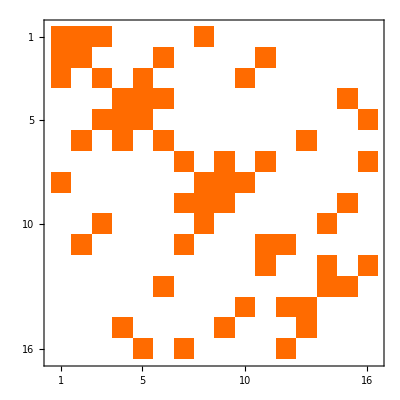
Adjacency matrix of orbit is: -Graphics-

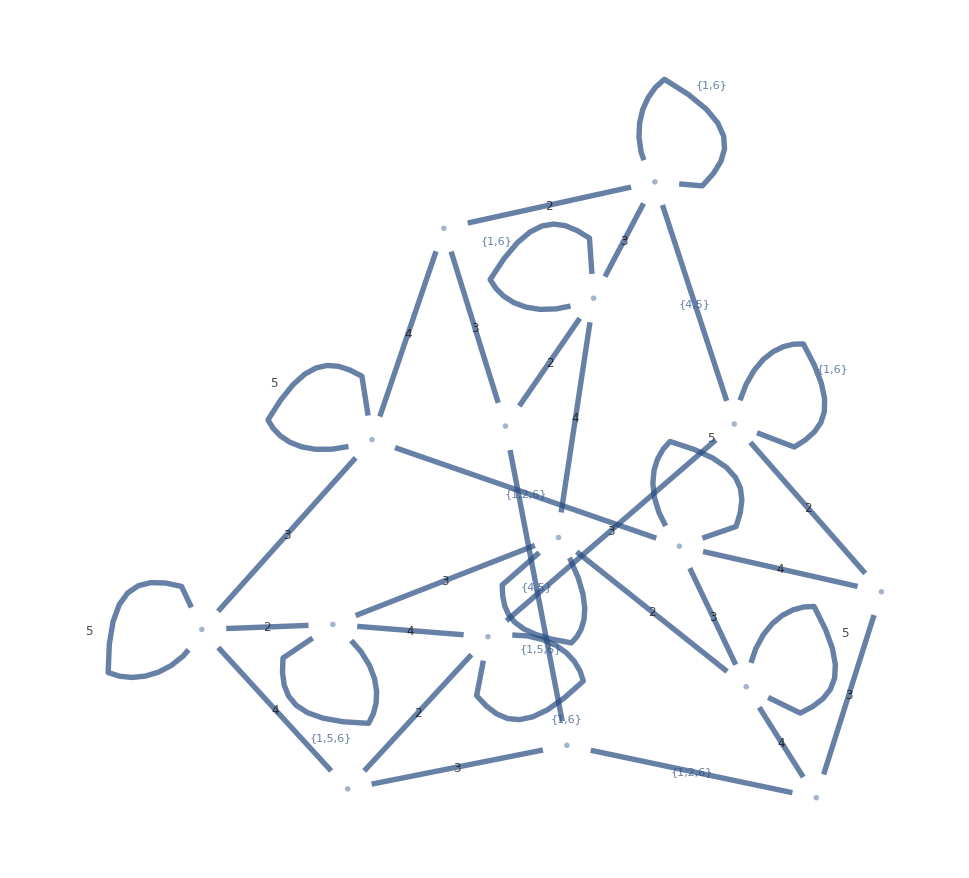

```mathematica
noqub=6;
myclass=4;

Print["First graph in orbit is: ",orbitsCigraphlist[[noqub]][[myclass]][[1]]]
Print["Number of graphs in Orbit is: ",Length@orbitsCigraphlist[[noqub]][[myclass]]]
Print["Adjacency matrix of orbit is: ",MatrixPlot@AdjacencyMatrix@orbitsCi[[noqub]][[myclass]]]

plotOrbitCi[noqub,myclass]
```

## Print labelled graph state orbitsCi adjacency matrices, ordered and grouped by graph state isomorphism

#### Compute colour space and edge labels

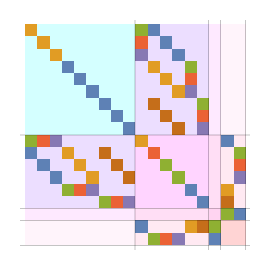
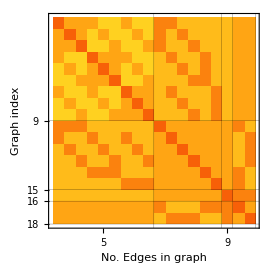
{-Graphics-,1 | RGBColor[0.368417, 0.506779, 0.709798]
2 | RGBColor[0.880722, 0.611041, 0.142051]
3 | RGBColor[0.560181, 0.691569, 0.194885]
4 | RGBColor[0.922526, 0.385626, 0.209179]
5 | RGBColor[0.528488, 0.470624, 0.701351]
6 | RGBColor[0.772079, 0.431554, 0.102387],-Graphics-,}

```mathematica
(*Adjust plot cosmetics*)
myframethickness=0.5;
myfontsize=10;
graphsize=270;

(*Adjust colour space for plots*)
satmod=0.17;
brightmod=1;

(*Difference in edge number required to be displayed on the plot*)
tickthresno=1;          (*in graph index*)
tickthresedge=1;     (*in edge number*)


plotOrbitMatrixCi[noqub,myclass]
```

# Exporter (used to generate .csv data)

## Four qubits

```mathematica
(*fourorbits=Table[StringReplace[ToString@EdgeList@orbitsCi[[4]][[i]]," -> "->"-"],{i,Length@orbitsCi[[4]]}];
Do[fourorbits[[i]]= StringReplace[fourorbits[[i]],"{"->"("];
fourorbits[[i]]= StringReplace[fourorbits[[i]],"}"->")"];
,{i,Length@fourorbits}] ;

fourorbitlabels=Table[StringReplace[ToString@Sort@(List@@@PropertyValue[orbitsCi[[4]][[i]],EdgeLabels])," -> "->"-"],{i,Length@orbitsCi[[4]]}];
Do[fourorbitlabels[[i]]= StringReplace[fourorbitlabels[[i]],"{"->"("];
fourorbitlabels[[i]]= StringReplace[fourorbitlabels[[i]],"}"->")"];
,{i,Length@fourorbitlabels}] ;

fourgraphs=Range@Length@orbitsCi[[4]];
Do[fourgraphs[[i]]=ToString[EdgeList/@orbitsCigraphlist[[4]][[i]]];
fourgraphs[[i]]= StringReplace[fourgraphs[[i]]," <-> "->"-"];
fourgraphs[[i]]= StringReplace[fourgraphs[[i]],"{"->"("];
fourgraphs[[i]]= StringReplace[fourgraphs[[i]],"}"->")"];
,{i,Length@orbitsCi[[4]]}] ;

fourqubitclasses={3,4};

fournoclasses=Table[Length@orbitsCigraphlist[[4]][[i]],{i,Length@orbitsCigraphlist[[4]]}];

fourdats={fourqubitclasses,fournoclasses,fourorbits,fourorbitlabels,fourgraphs}ᵀ;

Export["4qubitorbitsCi.csv",fourdats,"CSV"]*)
```

4qubitorbitsCi.csv

## Five qubits

```mathematica
(*fiveorbits=Table[StringReplace[ToString@EdgeList@orbitsCi[[5]][[i]]," -> "->"-"],{i,Length@orbitsCi[[5]]}];
Do[fiveorbits[[i]]= StringReplace[fiveorbits[[i]],"{"->"("];
fiveorbits[[i]]= StringReplace[fiveorbits[[i]],"}"->")"];
,{i,Length@fiveorbits}] ;

fiveorbitlabels=Table[StringReplace[ToString@Sort@(List@@@PropertyValue[orbitsCi[[5]][[i]],EdgeLabels])," -> "->"-"],{i,Length@orbitsCi[[5]]}];
Do[fiveorbitlabels[[i]]= StringReplace[fiveorbitlabels[[i]],"{"->"("];
fiveorbitlabels[[i]]= StringReplace[fiveorbitlabels[[i]],"}"->")"];
,{i,Length@fiveorbitlabels}] ;

fivegraphs=Range@Length@orbitsCi[[5]];
Do[fivegraphs[[i]]=ToString[EdgeList/@orbitsCigraphlist[[5]][[i]]];
fivegraphs[[i]]= StringReplace[fivegraphs[[i]]," <-> "->"-"];
fivegraphs[[i]]= StringReplace[fivegraphs[[i]],"{"->"("];
fivegraphs[[i]]= StringReplace[fivegraphs[[i]],"}"->")"];
,{i,Length@orbitsCi[[5]]}] ;

fivequbitclasses=Range[5,8];

fivenoclasses=Table[Length@orbitsCigraphlist[[5]][[i]],{i,Length@orbitsCigraphlist[[5]]}];

fivedats={fivequbitclasses,fivenoclasses,fiveorbits,fiveorbitlabels,fivegraphs}ᵀ;

Export["5qubitorbitsCi.csv",fivedats,"CSV"]*)
```

5qubitorbitsCi.csv

## Six qubits

```mathematica
(*sixorbits=Table[StringReplace[ToString@EdgeList@orbitsCi[[6]][[i]]," -> "->"-"],{i,Length@orbitsCi[[6]]}];
Do[sixorbits[[i]]= StringReplace[sixorbits[[i]],"{"->"("];
sixorbits[[i]]= StringReplace[sixorbits[[i]],"}"->")"];
,{i,Length@sixorbits}] ;

sixorbitlabels=Table[StringReplace[ToString@Sort@(List@@@PropertyValue[orbitsCi[[6]][[i]],EdgeLabels])," -> "->"-"],{i,Length@orbitsCi[[6]]}];
Do[sixorbitlabels[[i]]= StringReplace[sixorbitlabels[[i]],"{"->"("];
sixorbitlabels[[i]]= StringReplace[sixorbitlabels[[i]],"}"->")"];
,{i,Length@sixorbitlabels}] ;

sixgraphs=Range@Length@orbitsCi[[6]];
Do[sixgraphs[[i]]=ToString[EdgeList/@orbitsCigraphlist[[6]][[i]]];
sixgraphs[[i]]= StringReplace[sixgraphs[[i]]," <-> "->"-"];
sixgraphs[[i]]= StringReplace[sixgraphs[[i]],"{"->"("];
sixgraphs[[i]]= StringReplace[sixgraphs[[i]],"}"->")"];
,{i,Length@orbitsCi[[6]]}] ;

sixqubitclasses=Range[9,19];

sixnoclasses=Table[Length@orbitsCigraphlist[[6]][[i]],{i,Length@orbitsCigraphlist[[6]]}];

sixdats={sixqubitclasses,sixnoclasses,sixorbits,sixorbitlabels,sixgraphs}ᵀ;

Export["6qubitorbitsCi.csv",sixdats,"CSV"]*)
```

6qubitorbitsCi.csv

## Seven qubits

```mathematica
(*sevenorbits=Table[StringReplace[ToString@EdgeList@orbitsCi[[7]][[i]]," -> "->"-"],{i,Length@orbitsCi[[7]]}];
Do[sevenorbits[[i]]= StringReplace[sevenorbits[[i]],"{"->"("];
sevenorbits[[i]]= StringReplace[sevenorbits[[i]],"}"->")"];
,{i,Length@sevenorbits}] ;

sevenorbitlabels=Table[StringReplace[ToString@Sort@(List@@@PropertyValue[orbitsCi[[7]][[i]],EdgeLabels])," -> "->"-"],{i,Length@orbitsCi[[7]]}];
Do[sevenorbitlabels[[i]]= StringReplace[sevenorbitlabels[[i]],"{"->"("];
sevenorbitlabels[[i]]= StringReplace[sevenorbitlabels[[i]],"}"->")"];
,{i,Length@sevenorbitlabels}] ;

sevengraphs=Range@Length@orbitsCi[[7]];
Do[sevengraphs[[i]]=ToString[EdgeList/@orbitsCigraphlist[[7]][[i]]];
sevengraphs[[i]]= StringReplace[sevengraphs[[i]]," <-> "->"-"];
sevengraphs[[i]]= StringReplace[sevengraphs[[i]],"{"->"("];
sevengraphs[[i]]= StringReplace[sevengraphs[[i]],"}"->")"];
,{i,Length@orbitsCi[[7]]}] ;

sevenqubitclasses=Range[20,45];

sevennoclasses=Table[Length@orbitsCigraphlist[[7]][[i]],{i,Length@orbitsCigraphlist[[7]]}];

sevendats={sevenqubitclasses,sevennoclasses,sevenorbits,sevenorbitlabels,sevengraphs}ᵀ;

Export["7qubitorbitsCi.csv",sevendats,"CSV"]*)
```

7qubitorbitsCi.csv

## Eight qubits

```mathematica
(*eightorbits=Table[StringReplace[ToString@EdgeList@orbitsCi[[8]][[i]]," -> "->"-"],{i,Length@orbitsCi[[8]]}];
Do[eightorbits[[i]]= StringReplace[eightorbits[[i]],"{"->"("];
eightorbits[[i]]= StringReplace[eightorbits[[i]],"}"->")"];
,{i,Length@eightorbits}] ;

eightorbitlabels=Table[StringReplace[ToString@Sort@(List@@@PropertyValue[orbitsCi[[8]][[i]],EdgeLabels])," -> "->"-"],{i,Length@orbitsCi[[8]]}];
Do[eightorbitlabels[[i]]= StringReplace[eightorbitlabels[[i]],"{"->"("];
eightorbitlabels[[i]]= StringReplace[eightorbitlabels[[i]],"}"->")"];
,{i,Length@eightorbitlabels}] ;

eightgraphs=Range@Length@orbitsCi[[8]];
Do[eightgraphs[[i]]=ToString[EdgeList/@orbitsCigraphlist[[8]][[i]]];
eightgraphs[[i]]= StringReplace[eightgraphs[[i]]," <-> "->"-"];
eightgraphs[[i]]= StringReplace[eightgraphs[[i]],"{"->"("];
eightgraphs[[i]]= StringReplace[eightgraphs[[i]],"}"->")"];
,{i,Length@orbitsCi[[8]]}] ;

eightqubitclasses=Range[46,146];

eightnoclasses=Table[Length@orbitsCigraphlist[[8]][[i]],{i,Length@orbitsCigraphlist[[8]]}];

eightdats={eightqubitclasses,eightnoclasses, eightorbits,eightorbitlabels,eightgraphs}ᵀ;

Export["8qubitorbitsCi.csv",eightdats,"CSV"]*)
```

8qubitorbitsCi.csv